## Definiciones y gráficos iniciales

```mathematica
(* =========================================================*)
(*1. DEFINICIÓN DE INTEGRALES Y CORRIENTES DE CALOR*)
(* =========================================================*)

(*Unidades naturales:kB=1,h=1*)

(*Límite de truncamiento de la serie Trigamma *)
Nmax=150;

(*Integral I1 (Bosón L,Fermión R): *)
I1[TL_,TR_]:=(Pi^2/6)*TL^2-(Pi^2/12)*TR^2;

(*Integral I2: *)
(* I2[TL_,TR_]:=TL^2*Sum[(-1)^(n-1)*PolyGamma[1,1+n*TL/TR],{n,1,Nmax}]; *)
I2[TL_,TR_]:=TL^2*NSum[(-1)^(n-1)*PolyGamma[1,1+n*TL/TR],{n,1,Infinity},
Method->"AlternatingSigns",WorkingPrecision->20];

(*Corriente Térmica Híbrida (Bosón-Fermión)*)
Jhibrido[TL_,TR_]:=I1[TL,TR]-2*I2[TL,TR];

(*Conductancia Híbrida. Usamos un condicional (If) para el régimen lineal estricto 
(TL==TR) e inyectamos el resultado analítico exacto*)

Khibrido[TL_,TR_]:=If[TL==TR,(7*Zeta[3]/4)*TL,Jhibrido[TL,TR]/(TL-TR)];

(*Límite Simétrico Universal *)
J0[TL_,TR_]:=(Pi^2/6)*(TL^2-TR^2);

(*Conductancia cuántica universal K0*)
K0[TL_,TR_]:=(Pi^2/6)*(TL+TR);

(*Métrica de Comparación:Razón adimensional de conductancias*)
Eta[TL_,TR_]:=Khibrido[TL,TR]/K0[TL,TR];

(*Expresiones Alternativas*)

Jdiff[TL_,TR_]:= (Pi^2)*(TR^2)/12 -2*I2[TL,TR];

Kdiff[TL_,TR_]:= If[TL==TR,0,Jdiff[TL,TR]/(TL-TR)];

JdiffAsin[TL_,TR_]:= - 2*TL*TR*Log[2] + (Pi^2)*(TR^2)/6 ;

KdiffAsin[TL_,TR_]:= If[TL==TR,0,JdiffAsin[TL,TR]/(TL-TR)];

Jhibrido2[TL_,TR_]:= J0[TL,TR]+ Jdiff[TL,TR];
```

```mathematica
(* =========================================================*)
(*2. EVALUACIÓN PARA TEMPERATURAS DADAS*)
(* =========================================================*)
TLval=2.0;
TRval=1.0;

(*Cálculos de las corrientes*)
valJ0=J0[TLval,TRval];
valJdiff=Jdiff[TLval,TRval];
valJhibrida=valJ0+valJdiff;
valJhibrida2=Jhibrido[TLval, TRval];
valJdiffAsin=JdiffAsin[TLval,TRval];

(*Impresión de resultados estructurada*)
Print["=== Análisis de Corriente Térmica (TL = ",TLval,", TR = ",TRval,") ==="];
Print["1. Límite Simétrico (J0)    = ",NumberForm[valJ0,{6,4}]];
Print["2. Desviación Exacta (Jdiff) = ",NumberForm[valJdiff,{6,4}]];
Print["3. Corriente Híbrida (J = h(I_1 - 2I_2))     = ",NumberForm[valJhibrida,{6,4}]];
Print["3. Corriente Híbrida2 (J = J0 + Jdiff)     = ",NumberForm[valJhibrida2,{6,4}]];
Print["4. Corriente Hibrida asintótica (Jasin)     = ",NumberForm[valJdiffAsin,{6,4}]];
Print["-------------------------------------------------"];
Print["Fracción de transmisión (J/J0) = ",NumberForm[valJhibrida/valJ0*100,{4,2}],"%"];
```

NSum::precw: The precision of the argument function ((-1)^(n-1) PolyGamma[1,1+(n 2.)/1.]) is less than WorkingPrecision (20.).

=== Análisis de Corriente Térmica (TL = 2., TR = 1.) ===

1. Límite Simétrico (J0)    = 4.9348

2. Desviación Exacta (Jdiff) = -1.2709

3. Corriente Híbrida (J = h(I_1 - 2I_2))     = 3.6639

3. Corriente Híbrida2 (J = J0 + Jdiff)     = 3.6639

4. Corriente Hibrida asintótica (Jasin)     = -1.1277

-------------------------------------------------

Fracción de transmisión (J/J0) = 74.25%

```mathematica
TLval=10.0;
TRval=1.0;

(*Cálculos de las corrientes*)
valJ0=J0[TLval,TRval];
valJdiff=Jdiff[TLval,TRval];
valJhibrida=valJ0+valJdiff;
valJhibrida2=Jhibrido[TLval, TRval];
valJdiffAsin=JdiffAsin[TLval,TRval];

(*Impresión de resultados estructurada*)
Print["=== Análisis de Corriente Térmica (TL = ",TLval,", TR = ",TRval,") ==="];
Print["1. Límite Simétrico (J0)    = ",NumberForm[valJ0,{6,4}]];
Print["2. Desviación Exacta (Jdiff) = ",NumberForm[valJdiff,{6,4}]];
Print["3. Corriente Híbrida (J = h(I_1 - 2I_2))     = ",NumberForm[valJhibrida,{6,4}]];
Print["3. Corriente Híbrida2 (J = J0 + Jdiff)     = ",NumberForm[valJhibrida2,{6,4}]];
Print["4. Corriente Hibrida asintótica (Jasin)     = ",NumberForm[valJdiffAsin,{6,4}]];
Print["-------------------------------------------------"];
Print["Fracción de transmisión (J/J0) = ",NumberForm[valJhibrida/valJ0*100,{4,2}],"%"];
```

NSum::precw: The precision of the argument function ((-1)^(n-1) PolyGamma[1,1+(n 10.)/1.]) is less than WorkingPrecision (20.).

=== Análisis de Corriente Térmica (TL = 10., TR = 1.) ===

1. Límite Simétrico (J0)    = 162.8480

2. Desviación Exacta (Jdiff) = -12.2480

3. Corriente Híbrida (J = h(I_1 - 2I_2))     = 150.6000

3. Corriente Híbrida2 (J = J0 + Jdiff)     = 150.6000

4. Corriente Hibrida asintótica (Jasin)     = -12.2180

-------------------------------------------------

Fracción de transmisión (J/J0) = 92.48%

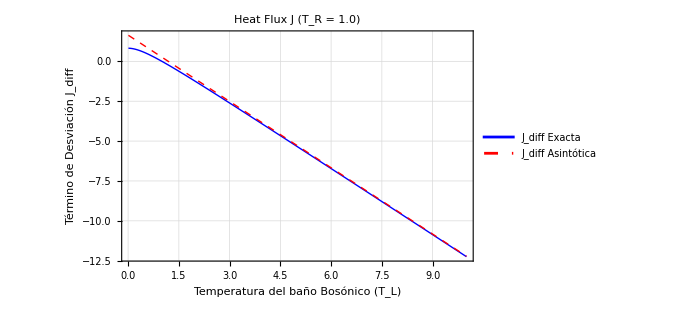

```mathematica
(* =========================================================*)
(*3. VISUALIZACIÓN DE LA DESVIACIÓN ESTADÍSTICA*)
(* =========================================================*)

TRFija=1.0;

Plot[{Jdiff[TL,TRFija],JdiffAsin[TL,TRFija]},{TL,0.01,10.0},
PlotStyle->{Directive[Thick,Blue],Directive[Thick,Dashed,Red]},PlotLegends->{"\!\(\*SubscriptBox[\(J\), \(diff\)]\) Exacta","\!\(\*SubscriptBox[\(J\), \(diff\)]\) Asintótica"},Frame->True,FrameLabel->{"Temperatura del baño Bosónico (\!\(\*SubscriptBox[\(T\), \(L\)]\))","Término de Desviación \!\(\*SubscriptBox[\(J\), \(diff\)]\)"},PlotLabel->"Heat Flux J (\!\(\*SubscriptBox[\(T\), \(R\)]\) = 1.0)",
GridLines->Automatic,BaseStyle->{FontSize->14}, 
ImageSize->500]
```

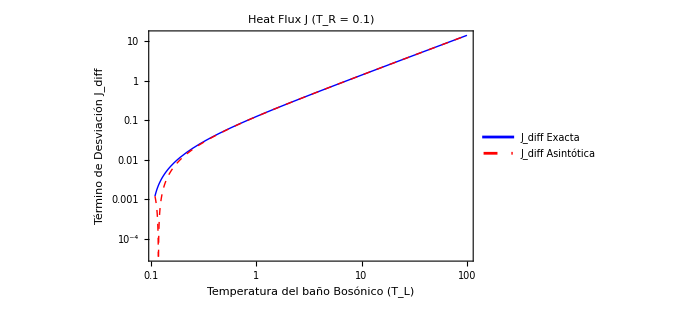

```mathematica
TRFija=0.1;

LogLogPlot[{Abs[Jdiff[TL,TRFija]],Abs[JdiffAsin[TL,TRFija]]},{TL,0.11,100.0},
PlotStyle->{Directive[Thick,Blue],Directive[Thick,Dashed,Red]},PlotLegends->{"\!\(\*SubscriptBox[\(J\), \(diff\)]\) Exacta","\!\(\*SubscriptBox[\(J\), \(diff\)]\) Asintótica"},Frame->True,FrameLabel->{"Temperatura del baño Bosónico (\!\(\*SubscriptBox[\(T\), \(L\)]\))","Término de Desviación \!\(\*SubscriptBox[\(J\), \(diff\)]\)"},PlotLabel->"Heat Flux J (\!\(\*SubscriptBox[\(T\), \(R\)]\) = 0.1)",
GridLines->Automatic,BaseStyle->{FontSize->14}, 
ImageSize->500]
```

```mathematica
TRFija=1.0;
```

NSum::precw: The precision of the argument function ((-1)^(n-1) PolyGamma[1,1+(n 0.0102041)/0.1]) is less than WorkingPrecision (20.).

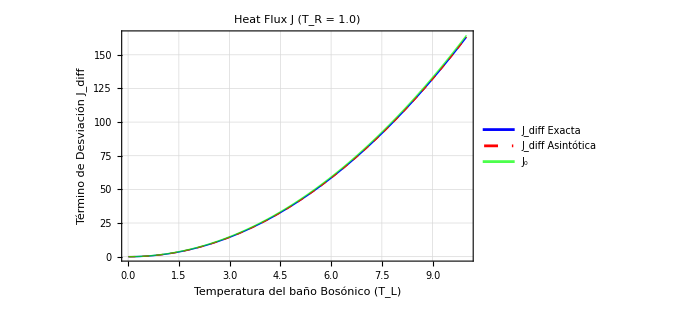

```mathematica
Plot[{Jhibrido[TL,TRFija],Jhibrido2[TL,TRFija], J0[TL,TRFija]  },{TL,0.01,10.0},
PlotStyle->{Directive[Thick,Blue],Directive[Thick,Dashed,Red], Directive[Thick, Green, Opacity[0.7]]},PlotLegends->{"\!\(\*SubscriptBox[\(J\), \(diff\)]\) Exacta","\!\(\*SubscriptBox[\(J\), \(diff\)]\) Asintótica","\!\(\*SubscriptBox[\(J\), \(0\)]\) " },Frame->True,FrameLabel->{"Temperatura del baño Bosónico (\!\(\*SubscriptBox[\(T\), \(L\)]\))","Término de Desviación \!\(\*SubscriptBox[\(J\), \(diff\)]\)"},PlotLabel->"Heat Flux J (\!\(\*SubscriptBox[\(T\), \(R\)]\) = 1.0)",
GridLines->Automatic,BaseStyle->{FontSize->14}, 
ImageSize->500]
```

NSum::precw: The precision of the argument function ((-1)^(n-1) PolyGamma[1,1+(n 5.0002)/4.9998]) is less than WorkingPrecision (20.).

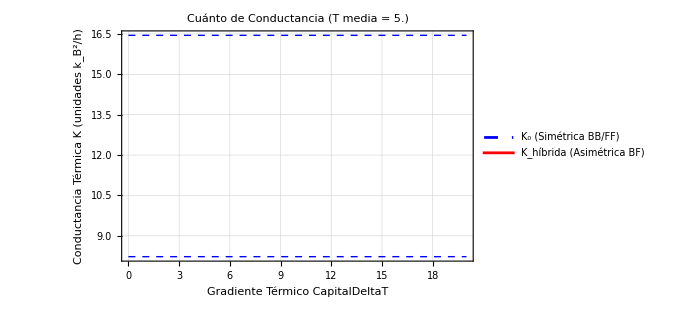

```mathematica
(* Fijamos la Temperatura Media de los baños *)
Tm = 5.0; 

(* Parametrización de TL y TR en función del gradiente DT *)
TL[DT_] := Tm + DT/2;
TR[DT_] := Tm - DT/2;

(* =========================================================*)
(*2. CONDUCTANCIA SIMÉTRICA (LÍNEA BASE CONSTANTE)*)
(* =========================================================*)
K0Constante=(Pi^2)/(3)*Tm;

Khibrido2[DT_]:=If[DT==0,(7*Zeta[3]/4)*Tm,Jhibrido[TL[DT],TR[DT]]/DT];

(*El dominio lógico de DT va desde 0 hasta 2*Tm (cuando TR=0)*)
(*Cortamos ligeramente antes de 2*Tm para evitar singularidad en TR=0*)

Plot[{K0Constante,Khibrido2[DT], K0Constante/2},{DT,0,20},PlotStyle->{Directive[Thick,Dashed,Blue],Directive[Thick,Red]},PlotLegends->Placed[{"\!\(\*SubscriptBox[\(K\), \(0\)]\) (Simétrica BB/FF)","\!\(\*SubscriptBox[\(K\), \(híbrida\)]\) (Asimétrica BF)"},Bottom],Frame->True,FrameLabel->{"Gradiente Térmico \!\(\*CapitalDelta\)T","Conductancia Térmica K (unidades \!\(\*SuperscriptBox[\(k_B\), \(2\)]\)/h)"},PlotLabel->"Cuánto de Conductancia (T media = "<>ToString[Tm]<>")",GridLines->Automatic,BaseStyle->{FontSize->14},PlotRange->All, ImageSize->500]
```

## Integrales individuales

```mathematica
Tm = 1.0;
```

NSum::precw: The precision of the argument function ((-1)^(n-1) PolyGamma[1,1+(n 1.00002)/0.99998]) is less than WorkingPrecision (20.).

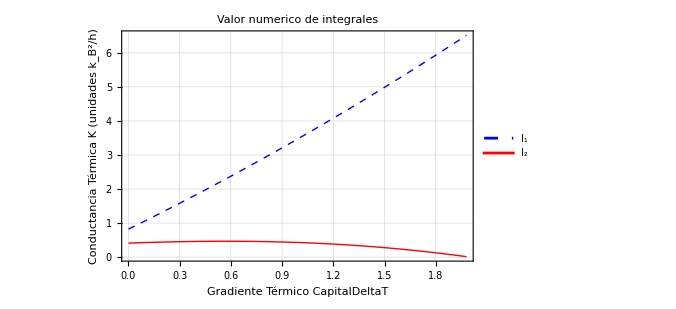

```mathematica
Plot[{I1[TL[DT], TR[DT]],I2[TL[DT], TR[DT]]},{DT,0,1.98*Tm},PlotStyle->{Directive[Thick,Dashed,Blue],Directive[Thick,Red]},PlotLegends->Placed[{"\!\(\*SubscriptBox[\(I\), \(1\)]\)","\!\(\*SubscriptBox[\(I\), \(2\)]\)"},Bottom],Frame->True,FrameLabel->{"Gradiente Térmico \!\(\*CapitalDelta\)T","Conductancia Térmica K (unidades \!\(\*SuperscriptBox[\(k_B\), \(2\)]\)/h)"},PlotLabel->"Valor numerico de integrales",GridLines->Automatic,BaseStyle->{FontSize->14},PlotRange->All, ImageSize->500]
```

## Otros gráficos

NSum::precw: The precision of the argument function ((-1)^(n-1) PolyGamma[1,1+(n 1.00052)/0.99948]) is less than WorkingPrecision (20.).

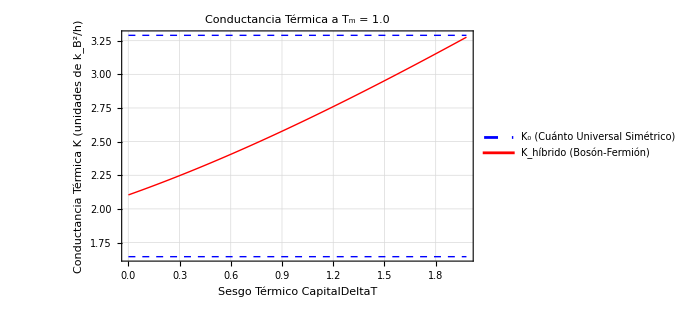

```mathematica
(* =========================================================*)
(*3. VISUALIZACIÓN 2D:CONDUCTANCIA VS SESGO TÉRMICO*)
(* =========================================================*)
(*Temperatura media del sistema fijada*)

Tm=1.0;

(*Parametrización en función de la media y el sesgo DeltaT*)
TL[DeltaT_]:=Tm+DeltaT/2;
TR[DeltaT_]:=Tm-DeltaT/2;

plotTransversal=Plot[{K0[TL[DT],TR[DT]],Khibrido[TL[DT],TR[DT]], K0[TL[DT],TR[DT]]/2},{DT,0.001,1.98*Tm},
PlotStyle->{Directive[Thick,Dashed,Blue],Directive[Thick,Red]},
PlotLegends->Placed[{"\!\(\*SubscriptBox[\(K\), \(0\)]\) (Cuánto Universal Simétrico)",
"\!\(\*SubscriptBox[\(K\), \(híbrido\)]\) (Bosón-Fermión)"},Bottom],
Frame->True,FrameLabel->{"Sesgo Térmico \!\(\*CapitalDelta\)T",
"Conductancia Térmica K  (unidades de \!\(\*SuperscriptBox[\(k_B\), \(2\)]\)/h)"},
PlotLabel->"Conductancia Térmica a \!\(\*SubscriptBox[\(T\), \(m\)]\) = 1.0",
BaseStyle->{FontSize->14},GridLines->Automatic, ImageSize->500]
```

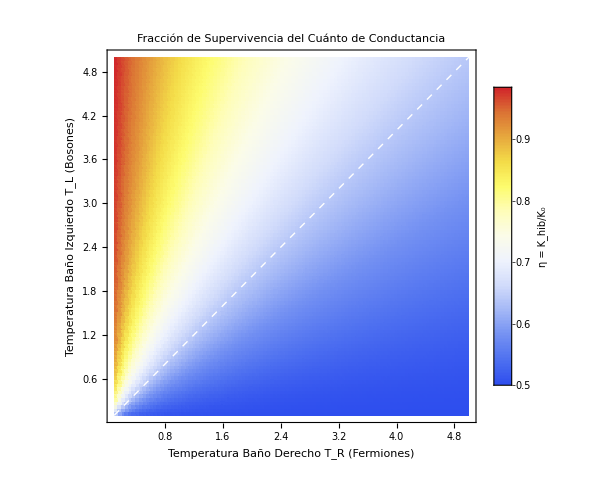

```mathematica
(* =========================================================*)
(*4. MAPEO DEL ESPACIO DE FASE DE LAS TEMPERATURAS*)
(* =========================================================*)

(*Definimos los límites térmicos y la resolución del grid*)

Tmin=0.1;
Tmax=5.0;
resolucion=100;

(*Generamos los datos en paralelo*)
datosEta=ParallelTable[{TR,TL,Eta[TL,TR]},
{TL,Tmin,Tmax,(Tmax-Tmin)/resolucion},
{TR,Tmin,Tmax,(Tmax-Tmin)/resolucion}];

(*Aplanamos la estructura tensorial a una simple lista de coordenadas {x,y,z}*)
datosPlanos=Flatten[datosEta,1];

(*Construimos el mapa de densidad*)
mapaDensidad=ListDensityPlot[datosPlanos,ColorFunction->"TemperatureMap",PlotLegends->BarLegend[Automatic,
LegendLabel->"η = \!\(\*SubscriptBox[\(K\), \(hib\)]\)/\!\(\*SubscriptBox[\(K\), \(0\)]\)"],FrameLabel->{"Temperatura Baño Derecho \!\(\*SubscriptBox[\(T\), \(R\)]\) (Fermiones)",
"Temperatura Baño Izquierdo \!\(\*SubscriptBox[\(T\), \(L\)]\) (Bosones)"},
PlotLabel->"Fracción de Supervivencia del Cuánto de Conductancia",
BoundaryStyle->None,BaseStyle->{FontSize->14},
(*Añadimos la línea diagonal punteada que representa el equilibrio termodinámico*)
Epilog->{Dashed,White,Thick,Line[{{Tmin,Tmin},{Tmax,Tmax}}]}, ImageSize->500]
```

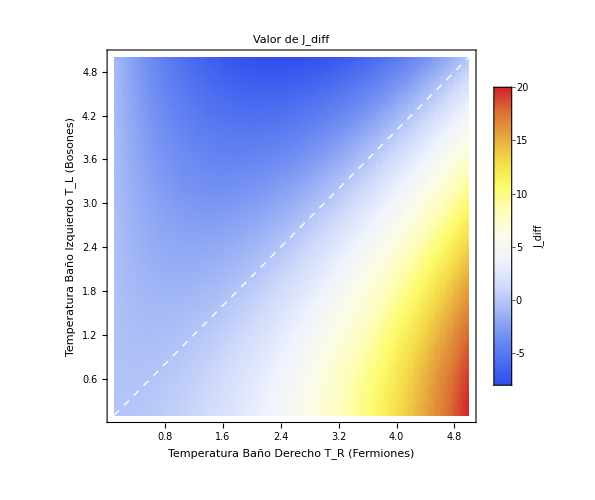

```mathematica
(*Generamos los datos en paralelo*)
datosEta=ParallelTable[{TR,TL,Jdiff[TL,TR]},
{TL,Tmin,Tmax,(Tmax-Tmin)/resolucion},
{TR,Tmin,Tmax,(Tmax-Tmin)/resolucion}];

(*Aplanamos la estructura tensorial a una simple lista de coordenadas {x,y,z}*)
datosPlanos=Flatten[datosEta,1];

(*Construimos el mapa de densidad*)
mapaDensidad=ListDensityPlot[datosPlanos,ColorFunction->"TemperatureMap",PlotLegends->BarLegend[Automatic,
LegendLabel->"J_diff"],FrameLabel->{"Temperatura Baño Derecho \!\(\*SubscriptBox[\(T\), \(R\)]\) (Fermiones)",
"Temperatura Baño Izquierdo \!\(\*SubscriptBox[\(T\), \(L\)]\) (Bosones)"},
PlotLabel->"Valor de J_diff",
BoundaryStyle->None,BaseStyle->{FontSize->14},
(*Añadimos la línea diagonal punteada que representa el equilibrio termodinámico*)
Epilog->{Dashed,White,Thick,Line[{{Tmin,Tmin},{Tmax,Tmax}}]}, ImageSize->500]
```

## Expansion en ordenes

NSum::precw: The precision of the argument function ((-1)^(n-1) PolyGamma[1,1+(n 1.01003)/1.]) is less than WorkingPrecision (20.).

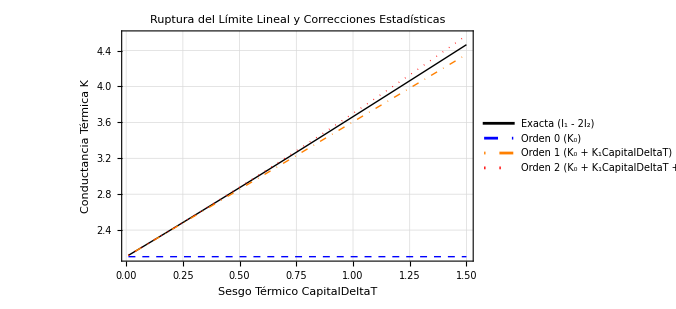

```mathematica
(* =========================================================*)
(*1. DEFINICIÓN DE COEFICIENTES ANALÍTICOS EXACTOS*)
(* =========================================================*)
(*Unidades naturales:kB=1,h=1*)

(*Coeficiente lineal *)
K00[T_]:=(7/4)*Zeta[3]*T;

(*Coeficiente de rectificación (Independiente de T)*)
K1:=(5/4)*Zeta[3];

(*Coeficiente no lineal de orden superior*)
K2[T_]:=(7/4*Zeta[3]-31/16*Zeta[5])/T;

(*Construcción de las aproximaciones de Taylor para la Conductancia*)
Kapprox0[T_,DT_]:=K00[T];
Kapprox1[T_,DT_]:=K00[T]+K1*DT;
Kapprox2[T_,DT_]:=K00[T]+K1*DT+K2[T]*DT^2;

(*Fijamos el baño frío en la temperatura base Tm y variamos solo TL*)
TL[DT_]:=Tm+DT;
TR[DT_]:=Tm;

Jhibrido[TL_,TR_]:=I1[TL,TR]-2*I2[TL,TR];
Khibrido2[DT_]:=If[DT==0,(7*Zeta[3]/4)*Tm,Jhibrido[TL[DT],TR[DT]]/DT];

(* =========================================================*)
(*3. VISUALIZACIÓN:CONVERGENCIA DE LA SERIE DE TAYLOR*)
(* =========================================================*)

(*Fijamos la temperatura del baño frío (TR=T)*)
Tm=1.0;

(*gráfico comparando la solución exacta con las aproximaciones*)
plotConvergencia=Plot[
{
Khibrido2[DT],
Kapprox0[Tm,DT],
Kapprox1[Tm,DT],
Kapprox2[Tm,DT]},
{DT,0.01,1.5*Tm},
PlotStyle->{Directive[Thick,Black],Directive[Thick,Dashed,Blue],Directive[Thick,DotDashed,Orange],Directive[Thick,Dotted,Red]},
PlotLegends->Placed[{
"Exacta (\!\(\*SubscriptBox[\(I\), \(1\)]\) - 2\!\(\*SubscriptBox[\(I\), \(2\)]\))","Orden 0 (\!\(\*SubscriptBox[\(K\), \(0\)]\))","Orden 1 (\!\(\*SubscriptBox[\(K\), \(0\)]\) + \!\(\*SubscriptBox[\(K\), \(1\)]\)\!\(\*CapitalDelta\)T)","Orden 2 (\!\(\*SubscriptBox[\(K\), \(0\)]\) + \!\(\*SubscriptBox[\(K\), \(1\)]\)\!\(\*CapitalDelta\)T + \!\(\*SubscriptBox[\(K\), \(2\)]\)\!\(\*SuperscriptBox[\(\!\(\*CapitalDelta\)T\), \(2\)]\))"},Right],
Frame->True,
FrameLabel->{"Sesgo Térmico \!\(\*CapitalDelta\)T","Conductancia Térmica K"},
PlotLabel->"Ruptura del Límite Lineal y Correcciones Estadísticas",
BaseStyle->{FontSize->14},
GridLines->Automatic,
PlotRange->All, ImageSize->500]
```

```mathematica
(*Generación de datos exactos en el régimen de perturbación pequeña*)
datosCorriente=Table[{DT,Jhibrido[Tbase,DT]},{DT,0.001,0.2,0.005}];

(*Ajuste polinomial de la corriente J=c1*DT+c2*DT^2+c3*DT^3*)
ajuste=LinearModelFit[datosCorriente,{x,x^2,x^3},x];

(*Extracción de coeficientes numéricos*)
coefsNumericos=ajuste["BestFitParameters"];

(*Comparación con nuestros hallazgos analíticos*)
Print["K0 Numérico: ",coefsNumericos[[2]]," | K0 Analítico: ",N[K0[Tbase]]];
Print["K1 Numérico: ",coefsNumericos[[3]]," | K1 Analítico: ",N[K1]];
Print["K2 Numérico: ",coefsNumericos[[4]]," | K2 Analítico: ",N[K2[Tbase]]];
```

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

Part::partw: Part 2 of LinearModelFit[{{0.001,Jhibrido[Tbase,0.001]},{0.006,Jhibrido[Tbase,0.006]},{0.011,Jhibrido[Tbase,0.011]},{0.016,Jhibrido[Tbase,0.016]},{0.021,Jhibrido[Tbase,0.021]},{0.026,Jhibrido[Tbase,0.026]},{0.031,Jhibrido[Tbase,0.031]},«27»,{0.171,Jhibrido[Tbase,0.171]},{0.176,Jhibrido[Tbase,0.176]},{0.181,Jhibrido[Tbase,0.181]},{0.186,Jhibrido[Tbase,0.186]},{0.191,Jhibrido[Tbase,0.191]},{0.196,Jhibrido[Tbase,0.196]}},{x,x^2,x^3},x][Bes…ters] does not exist.

K0 Numérico: LinearModelFit[{{0.001,Jhibrido[Tbase,0.001]},{0.006,Jhibrido[Tbase,0.006]},{0.011,Jhibrido[Tbase,0.011]},{0.016,Jhibrido[Tbase,0.016]},{0.021,Jhibrido[Tbase,0.021]},{0.026,Jhibrido[Tbase,0.026]},{0.031,Jhibrido[Tbase,0.031]},{0.036,Jhibrido[Tbase,0.036]},{0.041,Jhibrido[Tbase,0.041]},{0.046,Jhibrido[Tbase,0.046]},{0.051,Jhibrido[Tbase,0.051]},{0.056,Jhibrido[Tbase,0.056]},{0.061,Jhibrido[Tbase,0.061]},{0.066,Jhibrido[Tbase,0.066]},{0.071,Jhibrido[Tbase,0.071]},{0.076,Jhibrido[Tbase,0.076]},{0.081,Jhibrido[Tbase,0.081]},{0.086,Jhibrido[Tbase,0.086]},{0.091,Jhibrido[Tbase,0.091]},{0.096,Jhibrido[Tbase,0.096]},{0.101,Jhibrido[Tbase,0.101]},{0.106,Jhibrido[Tbase,0.106]},{0.111,Jhibrido[Tbase,0.111]},{0.116,Jhibrido[Tbase,0.116]},{0.121,Jhibrido[Tbase,0.121]},{0.126,Jhibrido[Tbase,0.126]},{0.131,Jhibrido[Tbase,0.131]},{0.136,Jhibrido[Tbase,0.136]},{0.141,Jhibrido[Tbase,0.141]},{0.146,Jhibrido[Tbase,0.146]},{0.151,Jhibrido[Tbase,0.151]},{0.156,Jhibrido[Tbase,0.156]},{0.161,Jhibrido[Tbase,0.161]},{0.166,Jhibrido[Tbase,0.166]},{0.171,Jhibrido[Tbase,0.171]},{0.176,Jhibrido[Tbase,0.176]},{0.181,Jhibrido[Tbase,0.181]},{0.186,Jhibrido[Tbase,0.186]},{0.191,Jhibrido[Tbase,0.191]},{0.196,Jhibrido[Tbase,0.196]}},{x,x^2,x^3},x][BestFitParameters]⟦2⟧ | K0 Analítico: K0[Tbase]

Part::partw: Part 3 of LinearModelFit[{{0.001,Jhibrido[Tbase,0.001]},{0.006,Jhibrido[Tbase,0.006]},{0.011,Jhibrido[Tbase,0.011]},{0.016,Jhibrido[Tbase,0.016]},{0.021,Jhibrido[Tbase,0.021]},{0.026,Jhibrido[Tbase,0.026]},{0.031,Jhibrido[Tbase,0.031]},«27»,{0.171,Jhibrido[Tbase,0.171]},{0.176,Jhibrido[Tbase,0.176]},{0.181,Jhibrido[Tbase,0.181]},{0.186,Jhibrido[Tbase,0.186]},{0.191,Jhibrido[Tbase,0.191]},{0.196,Jhibrido[Tbase,0.196]}},{x,x^2,x^3},x][Bes…ters] does not exist.

K1 Numérico: LinearModelFit[{{0.001,Jhibrido[Tbase,0.001]},{0.006,Jhibrido[Tbase,0.006]},{0.011,Jhibrido[Tbase,0.011]},{0.016,Jhibrido[Tbase,0.016]},{0.021,Jhibrido[Tbase,0.021]},{0.026,Jhibrido[Tbase,0.026]},{0.031,Jhibrido[Tbase,0.031]},{0.036,Jhibrido[Tbase,0.036]},{0.041,Jhibrido[Tbase,0.041]},{0.046,Jhibrido[Tbase,0.046]},{0.051,Jhibrido[Tbase,0.051]},{0.056,Jhibrido[Tbase,0.056]},{0.061,Jhibrido[Tbase,0.061]},{0.066,Jhibrido[Tbase,0.066]},{0.071,Jhibrido[Tbase,0.071]},{0.076,Jhibrido[Tbase,0.076]},{0.081,Jhibrido[Tbase,0.081]},{0.086,Jhibrido[Tbase,0.086]},{0.091,Jhibrido[Tbase,0.091]},{0.096,Jhibrido[Tbase,0.096]},{0.101,Jhibrido[Tbase,0.101]},{0.106,Jhibrido[Tbase,0.106]},{0.111,Jhibrido[Tbase,0.111]},{0.116,Jhibrido[Tbase,0.116]},{0.121,Jhibrido[Tbase,0.121]},{0.126,Jhibrido[Tbase,0.126]},{0.131,Jhibrido[Tbase,0.131]},{0.136,Jhibrido[Tbase,0.136]},{0.141,Jhibrido[Tbase,0.141]},{0.146,Jhibrido[Tbase,0.146]},{0.151,Jhibrido[Tbase,0.151]},{0.156,Jhibrido[Tbase,0.156]},{0.161,Jhibrido[Tbase,0.161]},{0.166,Jhibrido[Tbase,0.166]},{0.171,Jhibrido[Tbase,0.171]},{0.176,Jhibrido[Tbase,0.176]},{0.181,Jhibrido[Tbase,0.181]},{0.186,Jhibrido[Tbase,0.186]},{0.191,Jhibrido[Tbase,0.191]},{0.196,Jhibrido[Tbase,0.196]}},{x,x^2,x^3},x][BestFitParameters]⟦3⟧ | K1 Analítico: K1

Part::partw: Part 4 of LinearModelFit[{{0.001,Jhibrido[Tbase,0.001]},{0.006,Jhibrido[Tbase,0.006]},{0.011,Jhibrido[Tbase,0.011]},{0.016,Jhibrido[Tbase,0.016]},{0.021,Jhibrido[Tbase,0.021]},{0.026,Jhibrido[Tbase,0.026]},{0.031,Jhibrido[Tbase,0.031]},«27»,{0.171,Jhibrido[Tbase,0.171]},{0.176,Jhibrido[Tbase,0.176]},{0.181,Jhibrido[Tbase,0.181]},{0.186,Jhibrido[Tbase,0.186]},{0.191,Jhibrido[Tbase,0.191]},{0.196,Jhibrido[Tbase,0.196]}},{x,x^2,x^3},x][Bes…ters] does not exist.

K2 Numérico: LinearModelFit[{{0.001,Jhibrido[Tbase,0.001]},{0.006,Jhibrido[Tbase,0.006]},{0.011,Jhibrido[Tbase,0.011]},{0.016,Jhibrido[Tbase,0.016]},{0.021,Jhibrido[Tbase,0.021]},{0.026,Jhibrido[Tbase,0.026]},{0.031,Jhibrido[Tbase,0.031]},{0.036,Jhibrido[Tbase,0.036]},{0.041,Jhibrido[Tbase,0.041]},{0.046,Jhibrido[Tbase,0.046]},{0.051,Jhibrido[Tbase,0.051]},{0.056,Jhibrido[Tbase,0.056]},{0.061,Jhibrido[Tbase,0.061]},{0.066,Jhibrido[Tbase,0.066]},{0.071,Jhibrido[Tbase,0.071]},{0.076,Jhibrido[Tbase,0.076]},{0.081,Jhibrido[Tbase,0.081]},{0.086,Jhibrido[Tbase,0.086]},{0.091,Jhibrido[Tbase,0.091]},{0.096,Jhibrido[Tbase,0.096]},{0.101,Jhibrido[Tbase,0.101]},{0.106,Jhibrido[Tbase,0.106]},{0.111,Jhibrido[Tbase,0.111]},{0.116,Jhibrido[Tbase,0.116]},{0.121,Jhibrido[Tbase,0.121]},{0.126,Jhibrido[Tbase,0.126]},{0.131,Jhibrido[Tbase,0.131]},{0.136,Jhibrido[Tbase,0.136]},{0.141,Jhibrido[Tbase,0.141]},{0.146,Jhibrido[Tbase,0.146]},{0.151,Jhibrido[Tbase,0.151]},{0.156,Jhibrido[Tbase,0.156]},{0.161,Jhibrido[Tbase,0.161]},{0.166,Jhibrido[Tbase,0.166]},{0.171,Jhibrido[Tbase,0.171]},{0.176,Jhibrido[Tbase,0.176]},{0.181,Jhibrido[Tbase,0.181]},{0.186,Jhibrido[Tbase,0.186]},{0.191,Jhibrido[Tbase,0.191]},{0.196,Jhibrido[Tbase,0.196]}},{x,x^2,x^3},x][BestFitParameters]⟦4⟧ | K2 Analítico: K2[Tbase]

```mathematica
coefsNumericos[[2]]-N[K0[Tbase]]
```

0.00654446

```mathematica
coefsNumericos[[3]]  -  N[K1]
```

0.00238403

```mathematica
coefsNumericos[[4]]  - N[K2[Tbase]]
```

-0.0199491

## Articulo Karen

```mathematica
(*Sistema completamente Bosónico (+1,+1,+1)*)
KappaBoson[gL_,gR_,T_,w_]:=(w^2*gL^2*gR^2)/(gL^2+gR^2)*Csch[hbar*w/(2*kB*T)]^2/(4*kB*T^2);

(*Sistema completamente Fermiónico (-1,-1,-1)*)
KappaFermion[gL_,gR_,T_,w_]:=(w^2*gL^2*gR^2)/(gL^2+gR^2)*Sech[hbar*w/(2*kB*T)]^2/(4*kB*T^2);

(*Sistema Híbrido,Central Bosónico (+1,+1,-1)*)
KappaHibridoB[gL_,gR_,T_,w_]:=(w^2*gL^2*gR^2)/(gL^2*Coth[hbar*w/(2*kB*T)]+gR^2)*Csch[hbar*w/(2*kB*T)]^2/(4*kB*T^2);

(*Sistema Híbrido,Central Fermiónico (+1,-1,-1)*)
KappaHibridoF[gL_,gR_,T_,w_]:=(w^2*gL^2*gR^2)/(gL^2+gR^2*Tanh[hbar*w/(2*kB*T)])*Sech[hbar*w/(2*kB*T)]^2/(4*kB*T^2);
```

```mathematica
(* =========================================================*)
(*2. INTEGRACIÓN NUMÉRICA SOBRE TODAS LAS FRECUENCIAS*)
(* =========================================================*)
(*Parámetros físicos adimensionales*)
gLval=1.0;
gRval=1.0;
Tval=1.0;
hbar = 1.0;
kB = 1.0;

(*Integración numérica usando el método GlobalAdaptive para alta precisión*)
intBB=NIntegrate[KappaBoson[gLval,gRval,Tval,w],{w,0,Infinity},WorkingPrecision->15];
intFF=NIntegrate[KappaFermion[gLval,gRval,Tval,w],{w,0,Infinity},WorkingPrecision->15];
intBF=NIntegrate[KappaHibridoB[gLval,gRval,Tval,w],{w,0,Infinity},WorkingPrecision->15];
intFB=NIntegrate[KappaHibridoF[gLval,gRval,Tval,w],{w,0,Infinity},WorkingPrecision->15];

(* =========================================================*)
(*3. IMPRESIÓN Y COMPARACIÓN DE RESULTADOS*)
(* =========================================================*)

Print["--- Valores de la Integración Numérica (Modelo Colisional) ---"];
Print["BB (+1, +1, +1) = ",NumberForm[intBB,6]];
Print["FF (-1, -1, -1) = ",NumberForm[intFF,6]];
Print["BF (+1, +1, -1) = ",NumberForm[intBF,6]];
Print["FB (+1, -1, -1) = ",NumberForm[intFB,6]];
Print["K^(0) (expansion en ordenes) = ",NumberForm[K00[Tval],4]];
Print["K0 (universal) = ",NumberForm[K0Constante,4]];
Print[""];

Print["--- Fracciones de Transmisión respecto al límite BB ---"];
Print["FF / BB = ",NumberForm[intFF/intBB,4]];
Print["BF / BB = ",NumberForm[intBF/intBB,4]];
```

--- Valores de la Integración Numérica (Modelo Colisional) ---

BB (+1, +1, +1) = 1.64493

FF (-1, -1, -1) = 0.822467

BF (+1, +1, -1) = 1.20206

FB (+1, -1, -1) = 0.901543

K^(0) = 2.104

K0 (universal) = 3.29

--- Fracciones de Transmisión respecto al límite BB ---

FF / BB = 0.5000

BF / BB = 0.7308

Vamos a reescribir las expresiones para cada conductancia usando la variable x=hv/(k_B T) de manera que  v=(k_B T)/h x. De esta forma desaparecen todas las dimensiones y la comparación es mucho más limpia ya que las expresiones ahora se escriben (igualando las constantes uuniversales y la temperatura T a 1) como:

```mathematica
(*Sistema completamente Bosónico (+1,+1,+1)*)
KappaBoson[gL_,gR_,x_]:=((gL^2*gR^2)/(gL^2+gR^2))*((x^2*Csch[x/2]^2)/4);

(*Sistema completamente Fermiónico (-1,-1,-1)*)
KappaFermion[gL_,gR_,x_]:=((gL^2*gR^2)/(gL^2+gR^2))*((x^2*Sech[x/2]^2)/4);

(*Sistema Híbrido,Central Bosónico (+1,+1,-1)*)
KappaHibridoB[gL_,gR_,x_]:=((gL^2*gR^2)/(gL^2*Coth[x/2]+gR^2))*((x^2*Csch[x/2]^2)/4);

(*Sistema Híbrido,Central Fermiónico (+1,-1,-1)*)
KappaHibridoF[gL_,gR_,x_]:=((gL^2*gR^2)/(gL^2+Tanh[x/2]*gR^2))*((x^2*Sech[x/2]^2)/4);
```

En lugar de fijar los acoplamientos gL y gR, introducimos el cociente   r = g_R^2/g_L^2, de manera que

```mathematica
(*Sistema completamente Bosónico (+1,+1,+1)*)
KappaBoson[r_,x_]:=(r/(1+r))*((x^2*Csch[x/2]^2)/4);

(*Sistema completamente Fermiónico (-1,-1,-1)*)
KappaFermion[r_,x_]:=(r/(1+r))*((x^2*Sech[x/2]^2)/4);

(*Sistema Híbrido,Central Bosónico (+1,+1,-1)*)
KappaHibridoB[r_,x_]:=(r/(Coth[x/2]+r))*((x^2*Csch[x/2]^2)/4);

(*Sistema Híbrido,Central Fermiónico (+1,-1,-1)*)
KappaHibridoF[r_,x_]:=(r/(r*Tanh[x/2]+1))*((x^2*Sech[x/2]^2)/4);
```

```mathematica
(*Integración numérica usando el método GlobalAdaptive para alta precisión*)
intBB=NIntegrate[KappaBoson[1,x],{x,0,Infinity},WorkingPrecision->15];
intFF=NIntegrate[KappaFermion[1,x],{x,0,Infinity},WorkingPrecision->15];
intBF=NIntegrate[KappaHibridoB[1,x],{x,0,Infinity},WorkingPrecision->15];
intFB=NIntegrate[KappaHibridoF[1,x],{x,0,Infinity},WorkingPrecision->15];
```

```mathematica
Print["--- Valores de la Integración Numérica (Modelo Colisional) ---"];
Print["BB (+1, +1, +1) = ",NumberForm[intBB,6]];
Print["FF (-1, -1, -1) = ",NumberForm[intFF,6]];
Print["BF (+1, +1, -1) = ",NumberForm[intBF,6]];
Print["FB (+1, -1, -1) = ",NumberForm[intFB,6]];
Print[""];

Print["--- Fracciones de Transmisión respecto al límite BB ---"];
Print["FF / BB = ",NumberForm[intFF/intBB,4]];
Print["BF / BB = ",NumberForm[intBF/intBB,4]];
```

--- Valores de la Integración Numérica (Modelo Colisional) ---

BB (+1, +1, +1) = 1.64493

FF (-1, -1, -1) = 0.822467

BF (+1, +1, -1) = 1.20206

FB (+1, -1, -1) = 0.901543

--- Fracciones de Transmisión respecto al límite BB ---

FF / BB = 0.5000

BF / BB = 0.7308

```mathematica
rValues={10^-3,10^-2,10^-1,0.3,0.5,1,2,3,5,10,30,100,1000};
```

```mathematica
KBF[r_]:=NIntegrate[KappaHibridoB[r,x],{x,0,Infinity},WorkingPrecision->15,AccuracyGoal->10,PrecisionGoal->10];
```

```mathematica
datosBF=Table[{r,KBF[r]},{r,rValues}];
```

```mathematica
Grid[Prepend[datos,{"r","KBF(r)"}],Frame->All]
```

r | KBF(r)
1/1000 | 0.00164354898637537
1/100 | 0.0163119154004187
1/10 | 0.151745470046386
0.3 | 0.394577467908877
0.5 | 0.580891729364577
1 | 0.901542677369696
2 | 1.25037053852454
3 | 1.43875587097774
5 | 1.63960332220055
10 | 1.83671643140553
30 | 2.00327864813946
100 | 2.07178293878115
1000 | 2.10032514119151

```mathematica
(*limites analiticos*)
KSmall[r_]:=(7/4) Zeta[3] r;
KLarge=Pi^2/3;
```

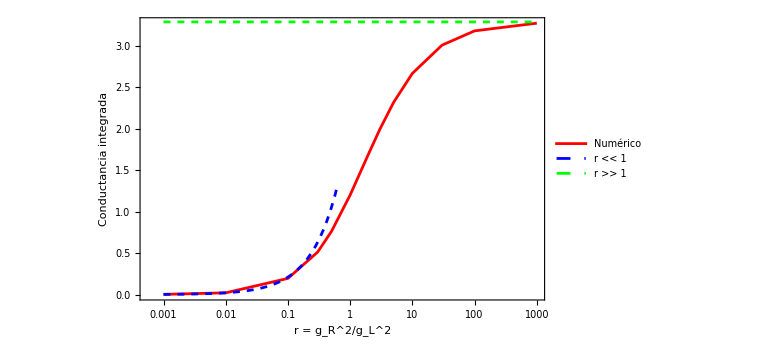

```mathematica
Show[
ListLogLinearPlot[datos,PlotStyle->{Red,PointSize[0.018]},Joined->True,PlotLegends->{"Numérico"}],LogLinearPlot[KSmall[r],{r,10^-3,1},PlotStyle->{Blue,Dashed},PlotLegends->{"r << 1"}],LogLinearPlot[KLarge,{r,10^-3,1000},PlotStyle->{Green,Dashed},PlotLegends->{"r >> 1"}],
Frame->True,FrameLabel->{Style["r = g_R^2/g_L^2",14],Style["Conductancia integrada",14]},
ImageSize->Large]
```

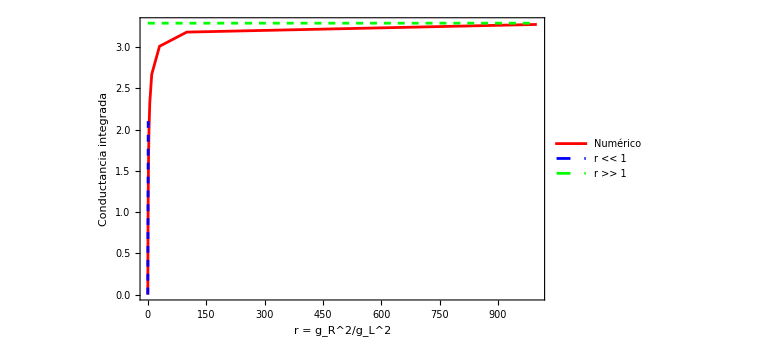

```mathematica
Show[
ListPlot[datos,PlotStyle->{Red,PointSize[0.018]},Joined->True,PlotLegends->{"Numérico"}],Plot[KSmall[r],{r,10^-3,1},PlotStyle->{Blue,Dashed},PlotLegends->{"r << 1"}],Plot[KLarge,{r,10^-3,1000},PlotStyle->{Green,Dashed},PlotLegends->{"r >> 1"}],
Frame->True,FrameLabel->{Style["r = g_R^2/g_L^2",14],Style["Conductancia integrada",14]},
ImageSize->Large, PlotRange-> All]
```

Para la sigiente gráfica vamos a normalizar el valor de KBF con respecto al limite bosónico K_BB = π^2/3. Como KBF alcanza dicho valor en el limite superior cuando r es grande, el grafico normalizado estará contenido entre cero y uno.

```mathematica
KBB=Pi^2/3;
datosNorm={#[[1]],#[[2]]/KBB}&/@datos;
```

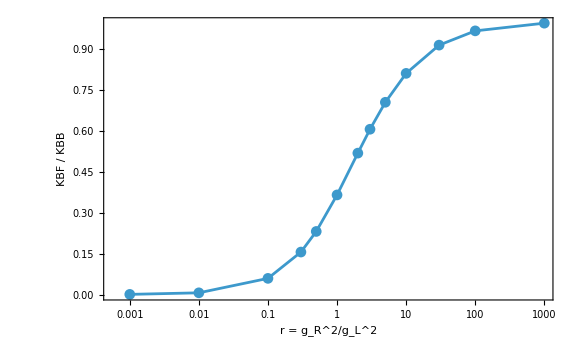

```mathematica
ListLogLinearPlot[datosNorm,
Joined->True,PlotMarkers->Automatic,Frame->True,
FrameLabel->{Style["r = g_R^2/g_L^2",14],Style["KBF / KBB",14]},
ImageSize->Large]
```

Analogamente, ahora vamos a normalizar con respecto al valor de KBF en el limite inferior de manera que la curva debe comenzar exactamente en 1. A medida que r aumenta, esa razón mostrará de forma muy clara cuándo deja de ser válida la aproximación lineal en r.

```mathematica
datosNorm2=Table[{r,KBF[r]/KSmall[r]},{r,rValues}];
```

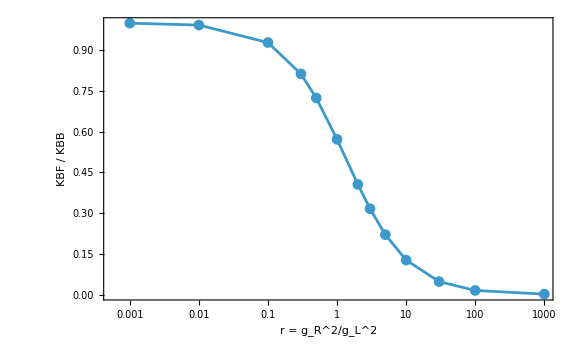

```mathematica
ListLogLinearPlot[datosNorm2,
Joined->True,PlotMarkers->Automatic,Frame->True,
FrameLabel->{Style["r = g_R^2/g_L^2",14],Style["KBF / KBB",14]},
ImageSize->Large]
```

### Caso Hibrido 2: (+1,-1,-1)

```mathematica
KappaHibridoF[r_,x_]:=(r/(r*Tanh[x/2]+1))*((x^2*Sech[x/2]^2)/4);
```

```mathematica
KBF2[r_]:=NIntegrate[KappaHibridoF[r,x],{x,0,Infinity},WorkingPrecision->15,AccuracyGoal->10,PrecisionGoal->10];
```

```mathematica
rValues={10^-3,10^-2,10^-1,0.3,0.5,1,2,3,5,10,30,100,1000};
datosFB=Table[{r,KBF2[r]},{r,rValues}];
Grid[Prepend[datos,{"r","KBF(r)"}],Frame->All]
```

r | KBF(r)
1/1000 | 0.00164354898637537
1/100 | 0.0163119154004187
1/10 | 0.151745470046386
0.3 | 0.394577467908877
0.5 | 0.580891729364577
1 | 0.901542677369696
2 | 1.25037053852454
3 | 1.43875587097774
5 | 1.63960332220055
10 | 1.83671643140553
30 | 2.00327864813946
100 | 2.07178293878115
1000 | 2.10032514119151

```mathematica
lim1[r_]:= (Pi^2 / 6 )r;
lim2[r_]:= 7/4 Zeta[3]
```

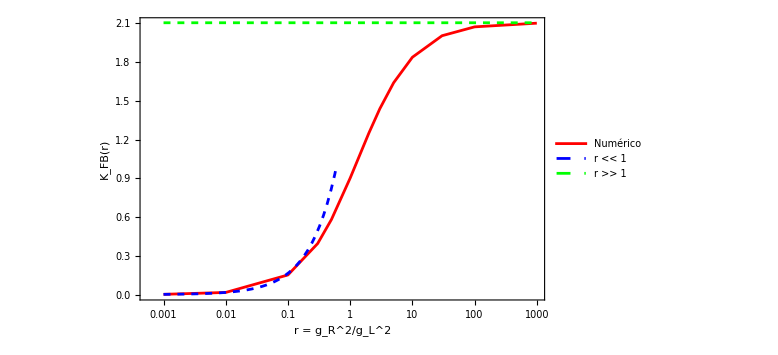

```mathematica
Show[
ListLogLinearPlot[datosFB,PlotStyle->{Red,PointSize[0.018]},Joined->True,PlotLegends->{"Numérico"}],LogLinearPlot[lim1[r],{r,10^-3,1},PlotStyle->{Blue,Dashed},PlotLegends->{"r << 1"}],LogLinearPlot[lim2[r],{r,10^-3,1000},PlotStyle->{Green,Dashed},PlotLegends->{"r >> 1"}],Frame->True,
FrameLabel->{Style["r = g_R^2/g_L^2",14],Style["K_FB(r)",14]},
ImageSize->Large]
```

```mathematica
KBB=Pi^2/3;
datosNormFB={#[[1]],#[[2]]/KBB}&/@datosFB;
```

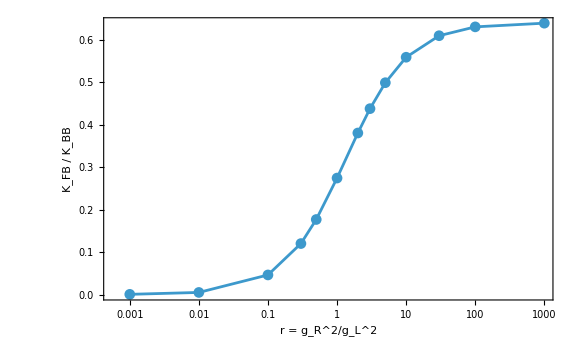

```mathematica
ListLogLinearPlot[datosNormFB,Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{Style["r = g_R^2/g_L^2",14],Style["K_FB / K_BB",14]},ImageSize->Large]
```

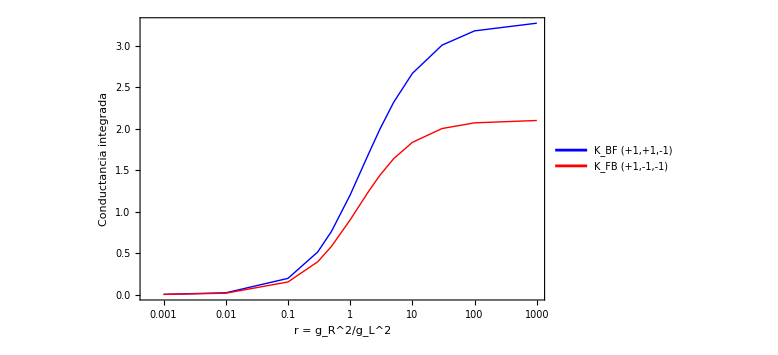

```mathematica
Show[
ListLogLinearPlot[datosBF,Joined->True,PlotStyle->{Blue,Thick}, PlotLegends->{"K_BF (+1,+1,-1)"}],
ListLogLinearPlot[datosFB,Joined->True,PlotStyle->{Red,Thick},  PlotLegends->{"K_FB (+1,-1,-1)"}],
Frame->True,FrameLabel->{Style["r = g_R^2/g_L^2",14],Style["Conductancia integrada",14]},
ImageSize->Large]
```